## Coupled fluid-field model

```mathematica
Quit
```

```mathematica
(* this is for pre-release only *)
pacletDir="/home/marco/Aveiro/Nerdy/Mathematica nbs/PTFB/PT2GW/";
(* pacletDir="/home/marco/Aveiro/Nerdy/Mathematica nbs/PTFB/Backup/TBounce_24-12-20" *)
PacletDirectoryLoad[pacletDir]
```

{/home/marco/Aveiro/Nerdy/Mathematica nbs/PTFB/PT2GW/}

## Initialize

Load PT2GW package and Example notebook:

```mathematica
<<PT2GW`
<<PT2GW/Examples.m
```

-Graphics-Name: | PT2GW
Version: | 0.2.0
Description: | Preparing to release.
WolframVersion: | 13.+
Creator: | Vedran Brdarhttps://inspirehep.net/authors/1495155Nonehttps://inspirehep.net/authors/1495155HyperlinkActionRecycledHyperlinkActive, Marco Finettihttps://inspirehep.net/authors/1892891Nonehttps://inspirehep.net/authors/1892891HyperlinkActionRecycledHyperlinkActive, Marco Matteinihttps://inspirehep.net/authors/2030238Nonehttps://inspirehep.net/authors/2030238HyperlinkActionRecycledHyperlinkActive, Antonio Moraishttps://inspirehep.net/authors/1066701Nonehttps://inspirehep.net/authors/1066701HyperlinkActionRecycledHyperlinkActive, Miha Nemevšekhttps://inspirehep.net/authors/1058763Nonehttps://inspirehep.net/authors/1058763HyperlinkActionRecycledHyperlinkActive

Energy units set to  1 GeV

✓ Imported Examples`

The coupled fluid-field model is defined by the potential

```mathematica
CFFModel[][ϕ,T]
```

1/2 γ (-T0^2+T^2) ϕ^2-1/3 A T ϕ^3+(λ ϕ^4)/4

Load the n^th benchmark

```mathematica
idx=3;
V=CFFModel[idx];
V[ϕ,T]
```

0.0555556 (-19600.+T^2) ϕ^2-0.00732009 T ϕ^3+0.000482253 ϕ^4

### Define parameters

Define bubble wall velocity:

```mathematica
vw=.9; (* units of c *)
```

#### Auxiliary parameters

Define energy units (defaults to GeV)
This defines the units of the 
- field
- temperature
- Planck mass M_P (entering the Hubble parameter)

```mathematica
DefineUnits["GeV"]
```

Energy units set to  1 GeV

Number of relativistic degrees of freedom (defaults to SM value at electroweak scale)

```mathematica
RelativisticDOF=106.75; (* RelativisticDOF is a TBounce package variable *)
```

Optional: define data required to compute bubble wall collision efficiency (κ_col).

```mathematica
(* this is the minimal data necessary to compute Subscript[κ, col] *)
colData={"GaugeCouplings"->{0.1},"MassFunctions"->{"Bosons"->{MassFunction[V]}},"T0"->"Tn","T"->"Tp"};
```

```mathematica
(* alternatively, one may define directly Subscript[κ, col] *)
(* colData={"κcol"->0.1} *)
```

## SearchPotential

To run a search for phase transitions, it is sufficient to provide the potential and bubble wall velocity

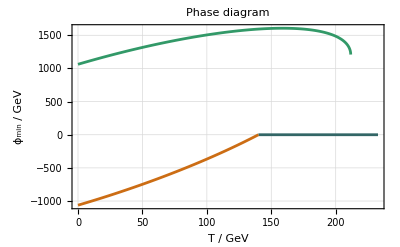

Looping over pairs of phases

Found transition at critical temperature

T_c  →  197.99 GeV

Computing nucleation temperature via Γ/H^4≈1 criterion and Bisection method...

T_n^estimate  →  148.231 GeVS_3/T → 149.073Γ/H^4 → 0.999352

Fitting action...

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindBounce::nosol: Solution not found, increase the number of segments or accuracy.

FindBounce::extrema: Wrong position of the extrema, check the minima or use "MidFieldPoint" to include the maximum/saddle point of the potential.

Action function →  ActionFunction[…]

T_n  →  147.946 GeVS_3/T → 141.212Γ/H^4 → 4037.03∫_T_n^T_c ⅆT/TΓ/H^4 → 0.999485

Computing phase transition parameters...

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

T_p  →  147.098 GeV

Percolation condition:  satisfied (-3.50036×10^-11)

T_transition →  Tp

α →   0.0849029

β/H →   3398.26

No GWs from bubble collisions: κ_col is Indeterminate. 
    Collisions' efficiency must be provided or computed via mass functions.

f^peak  →  0.0349579 Hz

h^2Ω_GW^peak →   3.71074×10^-16

Transition →  Transition[…]

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {PT2GW`Private`T} = {0.}.

```mathematica
transitions=SearchPotential[V,vw,
"TracingMethod"->NSolve,
"CollisionData"->None (* colData *),
"Metadata"->CFFModel[idx,"Benchmark"]//Normal (* optional: include metadata. Here we include the benchmark parameters. *),
"Plots"->"PhaseDiagram"
];//EchoTiming
```

47.332

### Inspect transition

Extract transition from list

```mathematica
tr=transitions[[1]]
AutoComplete[tr]; (* optional: quickly search keys from a drop-down menu *)
```

Transition[…]

Inspect transition elements

```mathematica
tr["ActionFunction"]
```

ActionFunction[…]

The key-search for Transitions behaves like Lookuppaclet:ref/Lookup[assoc,key,default,head]

```mathematica
tr[{"α","β/H","not a key"},"missing",Log10]
```

{-1.07108,3.53128,missing}

Display  all  data  as  Dataset

```mathematica
tr//Dataset
```

Get the underlying Association

```mathematica
tr//Normal
```

<|T0→140,γ→1/9,A→(√(5/2))/72,λ→0.00192901,Unit→GeV,RelativisticDOF→106.75,Phases→{Function[T,ConditionalExpression[0, 140.<T<211.66||T>211.66]],Function[T,ConditionalExpression[5.6921 T+9.77509×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.||140.<T<211.66]]},vw→0.9,Tc→197.99,TnEst→148.231,ActionFunction→ActionFunction[…],Domain→{140.,197.99},Tn→147.946,NucleationAction→141.212,NucleationDecayOverHubble→2405.42,NucleationIntegralDecay→0.999485,Tp→147.098,PercolationAction→120.431,PercolationIntegralValue→0.34,TpCondition→-3.50071×10^-11,α→0.0849028,β/H→3398.45,κcol→Indeterminate,Kcol→Indeterminate,αeff→0.0849028,κsw→0.133825,Ksw→0.00628376,fp→0.0091726,Treh→150.125,H*0→0.0000245368,HR→0.000775725,f1sw→0.00645637,f2sw→0.0450235,ε→0.5,𝒩→2,Ωs→0.00314188,f1mhd→0.000783527,f2mhd→0.0710201,Amhd→0.00435731,h2Omega→<|Soundwaves→((3.58532×10^-10 #1^3)/((1+23989.6 #1^2) (1+243356. #1^4))&),Turbulence→((3.10668×10^-11 #1^3)/((1+294.802 #1^2.15)^1.70543 √(1+2.65329×10^12 #1^4))&),Combined→(#1^3 ((3.58532×10^-10)/((1+23989.6 #1^2) (1+243356. #1^4))+(3.10668×10^-11)/((1+294.802 #1^2.15)^1.70543 √(1+2.65329×10^12 #1^4)))&)|>,fPeak→0.0349599,h2OmegaPeak→3.71029×10^-16|>

### Plots

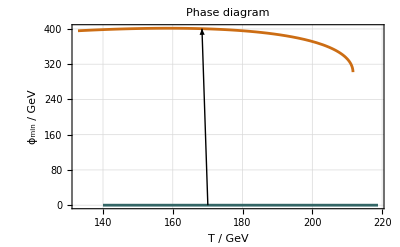

```mathematica
PlotTransition[tr]
```

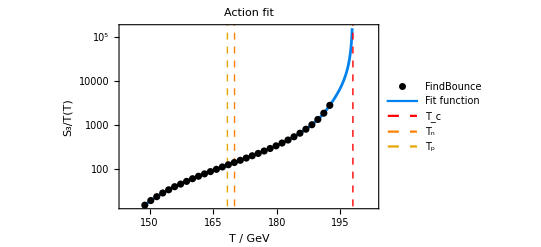

```mathematica
PlotAction[tr]
```

```mathematica
PlotGW[tr]
```

-Graphics-

## TBounce internal functions

All TBounce functions feature usage messages

```mathematica
?SearchPhases
```

A  template for the function arguments can be pasted from the popup menu (Ctrl+Shift+K, Cmd+Shift+K on Mac)

```mathematica
SearchPhases[V,{Subscript[ϕ, 1],Subscript[ϕ, 2]},Subscript[ξ, w]]
```

To list all TBounce functions , use

```mathematica
?TBounce`*
```

### Potential

Plot the potential, with dynamic temperature and field ranges

```mathematica
PlotPotential[V,2 10.^2{-1,3},100.,"LogTRange"->2.5,"LogϕRange"->2.]
```

Add sliders for the potential parameters

```mathematica
pot[ϕ_,T_,{γ_,A_,λ_,T0_}]:=CFFModel[][ϕ,T]/.{"γ"->γ,"A"->A,"λ"->λ,"T0"->T0}
```

```mathematica
Manipulate[Plot[pot[ϕ,T,{γ,A,λ,T0}],{ϕ,-ϕrange,2ϕrange}],
{{ϕrange,10^3},10,10^4},
{{T,200.},100.,300.},
{{γ,"γ"},0.,.5},
{{A,"A"},0.,.1},
{{λ,"λ"},0.,.1},
{{T0,"T0"},0.,200.}
]/.Normal[CFFModel[3,"Benchmark"]]//N
```

### ActionFit

Compute  action (calling FindBounce)

```mathematica
Action[tr["Tn"],V,tr["Phases"]]
```

140.957

Compute Euclidean action (calling FindBounce) and fit the action-temperature function S_3/T(T)

```mathematica
actionFunction=ActionFit[V,tr["Phases"],{150.,190.},tr["Tc"],
"Data"->None (*actionFunction["Data"] optional: pass action data if already computed *),
"Orders"->Range[-2,1] (* change the orders used in the Laurent polynomial fit function *)
]
```

ActionFunction[…]

Compare fit functions

{ActionFunction[…],ActionFunction[…]}

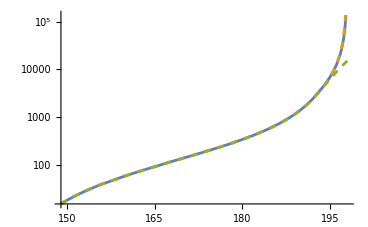

```mathematica
fits={};
AppendTo[fits,ActionFit[V,tr["Phases"],actionFunction["Domain"],tr["Tc"],"Data"->actionFunction["Data"]]]; (* default *) 
AppendTo[fits,ActionFit[V,tr["Phases"],actionFunction["Domain"],tr["Tc"],"Data"->actionFunction["Data"],"Orders"->Range[-3,0]]] (* different orders *)
AppendTo[fits,ActionFit[V,tr["Phases"],actionFunction["Domain"],tr["Tc"],"Data"->actionFunction["Data"],"ActionMethod"->Interpolation]]; (* other methods *)
LogPlot[Through[Through[fits["Function"]][T]]//Evaluate,{T,149.,198.},PlotStyle->{Dashing[None],Dashed,Dashed}]
```

### Nucleation temperature

Compute the nucleation rate

```mathematica
tr=CFFModel[1,"Transition"]
```

Transition[…]

```mathematica
DecayRate[tr["Tn"],V,tr["Phases"]]
```

5.39212×10^-51

Plot Γ/H^4(T)

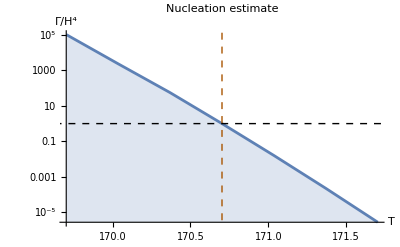

```mathematica
DiscretePlot[DecayOverHubble[T,V,tr["Phases"]],{T,Subdivide[tr["TnEst"]-1,tr["TnEst"]+1,6]},
AxesLabel->{"T","Γ/H^4"},PlotLabel->"Nucleation estimate",
"ScalingFunctions"->"Log",Joined->True,
Epilog->{Dashed,InfiniteLine[{0,Log@1},{1,0}],Darker@Orange,InfiniteLine[{tr["TnEst"],1},{0,1}]}]
```

Plot the nucleation criterion integral ∫_T^T_c ⅆT'/T' (Γ(T'))/(H^4(T')) (requires the action function)

```mathematica
actionFunction=tr["ActionFunction"]
```

ActionFunction[…]

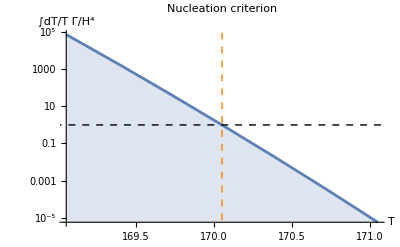

```mathematica
DiscretePlot[IntegralDecay[T,tr["Tc"],actionFunction["Function"],V,tr["Phases"]],{T,Subdivide[tr["Tn"]-1,tr["Tn"]+1,6]},
AxesLabel->{"T","∫dT/T Γ/H^4"},PlotLabel->"Nucleation criterion",
"ScalingFunctions"->"Log",Joined->True,Epilog->{Dashed,InfiniteLine[{0,Log@1},{1,0}],Orange,InfiniteLine[{tr["Tn"],1},{0,1}]}]
```

Estimate nucleation temperature

```mathematica
FindNucleation[V,{140.,190.},phases,"PrintIterations"->False,
Return->{"Tn","NucleationGammaOverH4"}
(*"NucleationCriterion"->{"ActionValue"->140.}*)
]//EchoTiming
```

7.05515

{148.229,1.00879}

```mathematica
DecayOverHubble[1.#,V,phases]&/@{142.}
```

{1.35305×10^54 If[0.00704225 $Failed[Action]<708.396,142.^4 ((0.00704225 $Failed[Action])/(2 π))^(3/2) ⅇ^(-(0.00704225 $Failed[Action])),0]}

```mathematica
FindNucleation[V,{149.,180.},phases,"PrintIterations"->True,
"NucleationCriterion"->"IntegraGammaOverH4",
"NucleationMethod"->{"ActionFunction"->tr["ActionFunction"]["Function"],"Tc"->tr["Tc"],"TnEst"->tr["TnEst"]},
Return->"Tn"
(*"NucleationCriterion"->{"ActionValue"->140.}*)
]//EchoTiming
```

Bad "NucleationCriterion"→"IntegraGammaOverH4" in FindTnuc.
Must match any of {GammaOverH4, IntegralGammaOverH4, {ActionValue :> Blank[]}}.

0.001728

Tn→Indeterminate

### Percolation temperature

Plot I_F=-log(P_F), where P_F is the false-vacuum fractional volume (requires the action function).
Explicitly, I_F(T)=(4π)/3 v_w^3∫_T^T_c ⅆT' (Γ(T'))/(H(T')T'^4)(∫_T^T' ⅆT''/(H(T'')))^3
The percolation temperature corresponds to I_F(T_p)≃0.34.

```mathematica
actionFunction=tr["ActionFunction"]
```

ActionFunction[…]

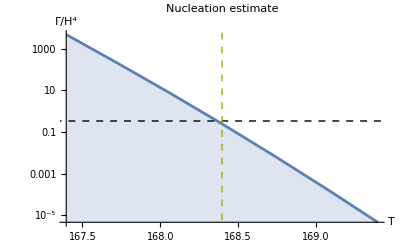

```mathematica
DiscretePlot[IFV[actionFunction["Function"],T,tr["Tc"],vw,V,tr["Phases"]],{T,Subdivide[tr["Tp"]-1,tr["Tp"]+1,6]},
AxesLabel->{"T","Γ/H^4"},PlotLabel->"Nucleation estimate",
"ScalingFunctions"->"Log",Joined->True,
Epilog->{Dashed,InfiniteLine[{0,Log@.34},{1,0}],Darker@Yellow,InfiniteLine[{tr["Tp"],1},{0,1}]}]
```

Determine the percolation temperature by solving I_F(T_p)=0.34

```mathematica
FindPercolation[actionFunction["Function"],{tr["Tn"],tr["Tc"]},vw,V,tr["Phases"]]
```

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

168.365

### Transition parameters

Compute the transition strength α≡1/ρ_γ Δ(V-T/4∂_T V), where Δ≡□_(false vac.)-□_(true vac.)

```mathematica
Alpha[tr["Tp"],V,tr["Phases"]]
Echo[tr["α"],"precomputed →"];
```

0.00154779

precomputed →  0.00154779

Compute the inverse duration in Hubble units β/H(T_*)≡(T_*[∂_T S_3/T])_(T_*)

```mathematica
BetaHubble[tr["Tp"],tr["ActionFunction"]["Function"]]
Echo[tr["β/H"],"precomputed →"];
```

1677.1

precomputed →  1677.1

### SearchPhases

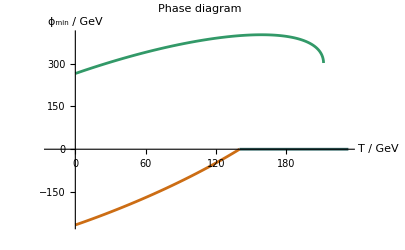

Phases →  Function[T,ConditionalExpression[0, 140.<T<211.66||T>211.66]]
Function[T,ConditionalExpression[1.42302 T-2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.]]
Function[T,ConditionalExpression[1.42302 T+2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.||140.<T<211.66]]

```mathematica
Phases=TracePhases[V,"TracingMethod"->NSolve]//
Echo[#,"Phases →",TableForm]&;
```

Found transition at critical temperature

T_c  →  197.99 GeV

Computing nucleation temperature via Γ/H^4≈1 criterion and Bisection method...

FindRoot::reged: The point {128.711} is at the edge of the search region {128.711,393.517} in coordinate 1 and the computed search direction points outside the region.

T_n^estimate  →  170.703 GeVS_3/T → 148.609Γ/H^4 → 1.00114

Fitting action...

Action function →  ActionFunction[…]

Computing nucleation temperature via ∫dT/T Γ/H^4≈1 criterion and action fit method...

T_n  →  170.052 GeVS_3/T → 140.957Γ/H^4 → 1976.62∫_T_n^T_c ⅆT/TΓ/H^4 → 0.999899

Computing phase transition parameters...

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

T_p  →  168.365 GeV

Percolation condition:  satisfied (-2.34432×10^-11)

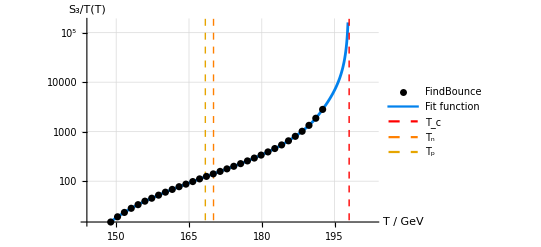

α →   0.00154779

β/H →   1677.12

f^peak  →  0.0193537 Hz

h^2Ω_GW^peak →   1.11648×10^-20

```mathematica
tr=SearchPhases[V,Phases[[{1,3}]],vw,
"NActionPoints"->31, (* optional: change the number of computations of the action *)
"CollisionData"->None (* colData *),
"Metadata"->CFFModel[1,"Benchmark"]//Normal,
"Plots"->{"Action"},
ProgressIndicator->False];//EchoTiming
```

30.3028

```mathematica
AutoComplete[tr]; (* optional: quickly access Transition keys from a drop-down menu *)
```

```mathematica
tr[Dataset]
```

## Gravitational waves

Load a Transition

```mathematica
tr=CFFModel[1,"Transition"]
AutoComplete[tr];
```

Transition[…]

#### κ collisions

```mathematica
mϕ=MassFunction[V];
mϕ[ϕ,T]
```

√(0.0555556 (-19600.+T^2)-0.088 T ϕ+0.045 ϕ^2)

```mathematica
phases=tr["Phases"]
```

{Function[Private`T,ConditionalExpression[0, 140.<Private`T<216.231||Private`T>216.231]],Function[Private`T,ConditionalExpression[1.46667 Private`T+0.108866 (6.125×10^6-131. (Private`T)^2)^Rational[1,2], 0<Private`T<140.||140.<Private`T<216.231]]}

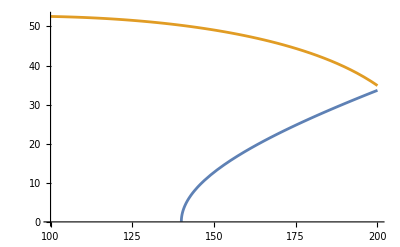

```mathematica
Plot[mϕ[#[T],T]&/@phases//Evaluate,{T,100,200}]
```

```mathematica
colData={"GaugeCouplings"->{0.1},"MassFunctions"->{"Bosons"->{mϕ}},"T0"->tr["Tn"],"T"->tr["Tp"]}
```

{GaugeCouplings→{0.1},MassFunctions→{Bosons→{Function[{TBounce`Private`ϕ$,TBounce`Private`T$},√(0.0555556 (-19600.+(TBounce`Private`T$)^2)-0.088 TBounce`Private`T$ TBounce`Private`ϕ$+0.045 (TBounce`Private`ϕ$)^2)]}},T0→170.821,T→169.087}

```mathematica
data=Append[KeyDrop[tr[Association],"κcol"],colData~Join~{"Potential"->V}];
```

κ_col function breakdown:

```mathematica
{T,T0}={"T","T0"}/.data
massFun=({"Fermions","Bosons"}/.("MassFunctions"/.data)/.{"Fermions"->{},"Bosons"->{}})
{Δmf,Δmv}=Map[#[phases[[2]][T],T]-#[phases[[1]][T],T]&,massFun,{2}]
{nf,nv}={"nF","nB"}/.data/.{"nF"->1,"nB"->1}(* number of fermions and bosons. Set to 1 if not defined. *)
gC="GaugeCouplings"/.data/.{}->0.
Δm2=Δm2Fun[Δmf,Δmv,nf,nv]
g2Δmv=g2ΔmvFun[gC,Δmv,nv]
α∞=α∞Fun[Δm2,T]
αeq=αeqFun[g2Δmv,T]
γeq=γeqFun[tr["α"],α∞,αeq]
γstar=γstarFun[tr["ActionFunction"],tr["β/H"],T,T0,V,phases,vw]
κCol=κColFun[γstar,γeq,tr["α"],α∞]
```

#### Compute SGWB

```mathematica
action=data["ActionFunction"]
```

ActionFunction[…]

```mathematica
κColFun[data,Return->{"κcol","Data"}]
```

{0.986116,<|Δmf→{},Δmv→{23.428},nF→1,nV→1,gaugeCoup→{0.1},Δm2→548.872,g2Δmv→0.23428,R0→3.80023×10^10,Rstar→4.51885×10^10,α∞→0.0000227767,αeq→0.0000394528,γeq→41.0043,γstar→0.792733|>}

```mathematica
ComputeSGWB[tr[Association],"CollisionData"->data]//Dataset
```

```mathematica
PlotGW[GWData["h2Omega"]]
```

-Graphics-

```mathematica
Options@ComputeSGWB
```

{CollisionData→None,Sources→{Collisions,Soundwaves,Turbulence,Combined},SoundSpeed→1/(√3),ε→0.5,𝒩→2,ShapeParameters→}

```mathematica
PlotGW[GWData["h2Omega"],PlotRange->{10^{-7,5},10^{-50,-18}}]
```

-Graphics-

```mathematica
GWData["h2Omega"]
```

GWData[h2Omega]

```mathematica
GWData//Dataset
```

#### Detector sensitivities

To add a user-defined detector sensitivity, simply  define the corresponding PISC (peak-integrated sensitivity curve), as a function of frequency in Hertz:

```mathematica
PISC[f_,"myDetector"]:=10^-22 (10^3 f^2+10^-3 f^-2)
```

```mathematica
PlotGW[tr,"Detectors"->{"myDetector"}]
```

-Graphics-

## Parameter-space scan

```mathematica
transitions={};
```

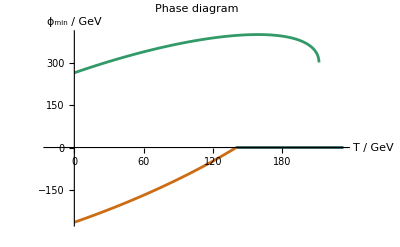

FindRoot::reged: The point {128.711} is at the edge of the search region {128.711,393.517} in coordinate 1 and the computed search direction points outside the region.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {TBounce`Private`T} = {0.}.

```mathematica
Scan[(V=CFFModel[#];
tr=SearchPotential[V,vw,"TracingMethod"->NSolve,
"CollisionData"->None,
"Metadata"->CFFModel[#,"Benchmark"]//Normal,
"Plots"->{"PhaseDiagram"}]//EchoTiming;
If[MatchQ[tr,{_Transition}],AppendTo[transitions,tr[[1]]]];
)&,
Range[7]]
```

27.8107

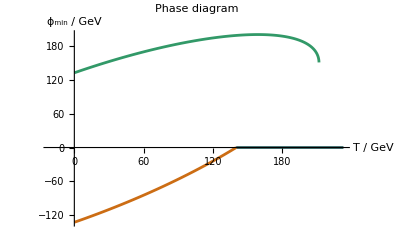

FindRoot::reged: The point {78.1387} is at the edge of the search region {78.1387,193.287} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {74.9903} is at the edge of the search region {74.9903,194.183} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {TBounce`Private`T} = {0.}.

39.5913

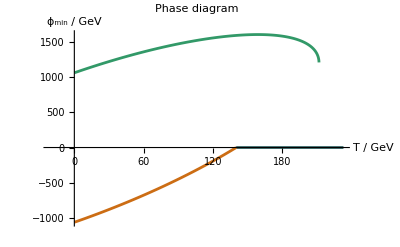

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindBounce::nosol: Solution not found, increase the number of segments or accuracy.

FindBounce::extrema: Wrong position of the extrema, check the minima or use "MidFieldPoint" to include the maximum/saddle point of the potential.

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {TBounce`Private`T} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

35.4841

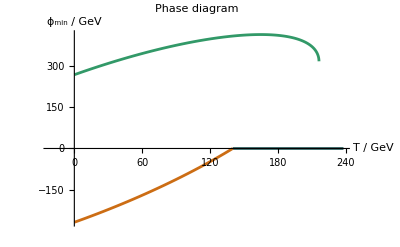

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

31.3273

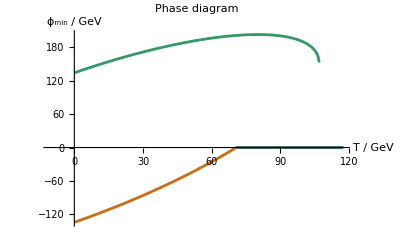

35.1257

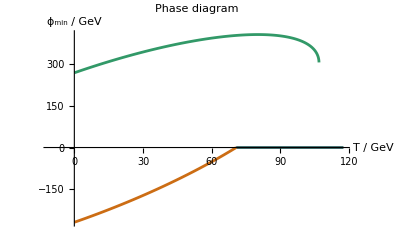

FindBounce::extrema: Wrong position of the extrema, check the minima or use "MidFieldPoint" to include the maximum/saddle point of the potential.

52.3799

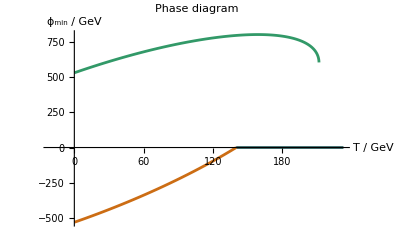

FindBounce::extrema: Wrong position of the extrema, check the minima or use "MidFieldPoint" to include the maximum/saddle point of the potential.

General::stop: Further output of FindBounce::extrema will be suppressed during this calculation.

51.1614

```mathematica
transitions
```

{Transition[…],Transition[…],Transition[…],Transition[…],Transition[…],Transition[…],Transition[…]}

## Load/Save data

### Load the coupled fluid-field model

The CFFModel is defined as

```mathematica
CFFModel[]
```

Function[{ϕ,T},1/2 γ (T^2-T0^2) ϕ^2-1/3 A T ϕ^3+(λ ϕ^4)/4]

You  can load specific benchmarks by passing an index argument

```mathematica
idx=3;
V=CFFModel[idx];
V[ϕ,T]
```

0.0555556 (-19600.+T^2) ϕ^2-0.00732009 T ϕ^3+0.000482253 ϕ^4

To list the default benchmark parameters, use the “Benchmark” argument

```mathematica
CFFModel[All,"Benchmark"]
```

Benchmark parameters can be defined as Associations

```mathematica
bp=<|"T0"->140,"γ"->1/18,"A"->(√(5/2))/36,"λ"->5/324|>;
V=CFFModel[]/.bp
```

Function[{ϕ,T},((T^2-140^2) ϕ^2)/(18 2)-(√(5/2) T ϕ^3)/(36 3)+(5 ϕ^4)/(324 4)]

### Load a CFF transition

The transitions corresponding to the benchmark parameters above can be loaded with the “Transition” argument

```mathematica
tr=CFFModel[idx,"Transition"]
```

Transition[…]

### Save a transition

As an example, here we save a Transition object to a .m file in the notebook directory

```mathematica
SetDirectory[NotebookDirectory[]];
tr>>transition_CFF.m
```

The same transition can then be loaded with

```mathematica
tr=<<transition_CFF.m
```

Transition[…]